```mathematica
Integrate[2/(π p k)Sin[p r]Exp[-(r/R)^4]Sin[k r],{r,0,∞},Assumptions->{p>0,k>0,R>0}]
```

1/(32 k p π)(8 R Gamma[1/4] (HypergeometricPFQ[{},{1/2,3/4},1/256 (k-p)^4 R^4]-HypergeometricPFQ[{},{1/2,3/4},1/256 (k+p)^4 R^4])+R^3 Gamma[-1/4] ((k-p)^2 HypergeometricPFQ[{},{5/4,3/2},1/256 (k-p)^4 R^4]-(k+p)^2 HypergeometricPFQ[{},{5/4,3/2},1/256 (k+p)^4 R^4]))

```mathematica
Integrate[2/(π p k)Sin[p r] 1/r^4 Sin[k r],{r,R,∞},Assumptions->{p>0,k>0,R>0}]
```

1/(12 k p π R^3)(-k^3 π R^3-3 k^2 p π R^3-3 k p^2 π R^3-p^3 π R^3+(k-p)^2 π R^3 Abs[k-p]+8 k p R^2 Cos[k R] Cos[p R]+4 p R Cos[p R] Sin[k R]+4 k R Cos[k R] Sin[p R]+8 Sin[k R] Sin[p R]-4 k^2 R^2 Sin[k R] Sin[p R]-4 p^2 R^2 Sin[k R] Sin[p R]-2 (k-p)^3 R^3 SinIntegral[(k-p) R]+2 k^3 R^3 SinIntegral[(k+p) R]+6 k^2 p R^3 SinIntegral[(k+p) R]+6 k p^2 R^3 SinIntegral[(k+p) R]+2 p^3 R^3 SinIntegral[(k+p) R])

```mathematica
1/(32 k p π)(8 R Gamma[1/4] (HypergeometricPFQ[{},{1/2,3/4},1/256 (k-p)^4 R^4]-HypergeometricPFQ[{},{1/2,3/4},1/256 (k+p)^4 R^4])+R^3 Gamma[-1/4] ((k-p)^2 HypergeometricPFQ[{},{5/4,3/2},1/256 (k-p)^4 R^4]-(k+p)^2 HypergeometricPFQ[{},{5/4,3/2},1/256 (k+p)^4 R^4]))/.{p->k}
```

```mathematica
FullSimplify[1/(32 k^2 π)(8 R Gamma[1/4] (1-HypergeometricPFQ[{},{1/2,3/4},(k^4 R^4)/16])-4 k^2 R^3 Gamma[-1/4] HypergeometricPFQ[{},{5/4,3/2},(k^4 R^4)/16])]
```

```mathematica
FullSimplify[1/(8 π)R (-(8 Gamma[5/4] (-1+HypergeometricPFQ[{},{1/2,3/4},(k^4 R^4)/16]))/k^2-R^2 Gamma[-1/4] HypergeometricPFQ[{},{5/4,3/2},(k^4 R^4)/16])/.k->x/R]
```

```mathematica
Series[(R^3 (-(8 Gamma[5/4] (-1+HypergeometricPFQ[{},{1/2,3/4},x^4/16]))/x^2-Gamma[-1/4] HypergeometricPFQ[{},{5/4,3/2},x^4/16]))/(8 π),{x,∞,3}]
```

Series::ztest1: Unable to decide whether numeric quantity -(2^(1/3) Gamma[-1/4] Gamma[5/4])/(√(3 π))-(4 2^(1/3) Gamma[3/4] Gamma[5/4])/(√(3 π)) is equal to zero. Assuming it is.

((R^3 Gamma[5/4])/(π x^2)+O[1/x]^4)+ⅇ^((3 x^(4/3))/(2 2^(1/3))+O[1/x]^(10/3)) (-((R^3 Gamma[-1/4] Gamma[5/4]) (1/x)^(7/3))/(4 (2^(2/3) √3 π^(3/2)))+O[1/x]^(10/3))+ⅇ^((3 x^(4/3))/(2 2^(1/3))+O[1/x]^(10/3)) (-(R^3 Gamma[3/4] Gamma[5/4] (1/x)^(7/3))/(2^(2/3) √3 π^(3/2))+O[1/x]^(10/3))

```mathematica
f[k_,R_]:=1/(32 k^2 π)(8 R Gamma[1/4] (1-HypergeometricPFQ[{},{1/2,3/4},(k^4 R^4)/16])-4 k^2 R^3 Gamma[-1/4] HypergeometricPFQ[{},{5/4,3/2},(k^4 R^4)/16]);
```

```mathematica
β = 33;μ = 240;
```

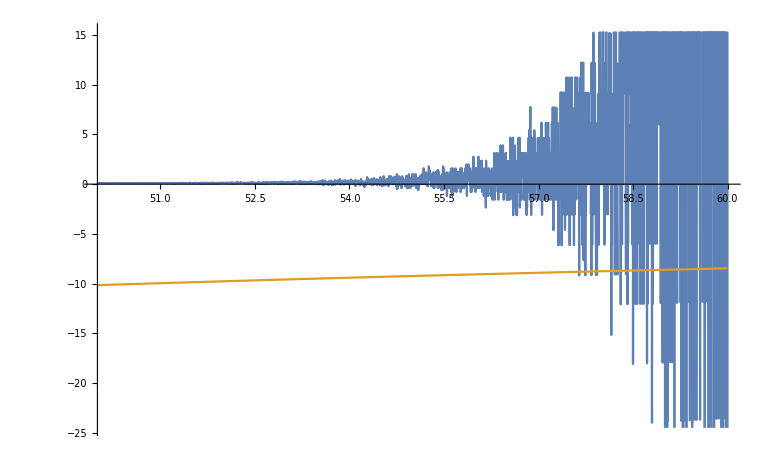

```mathematica
Plot[{-2μ kβ/β(-0.00013668)f[kβ/β,β/4],-2 μ kβ/β (0.02493599)f[kβ/β,β/7.4]},{kβ,50,60}]
```

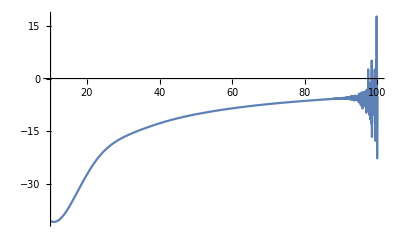

```mathematica
Plot[-2 μ kβ/β (0.02493599)f[kβ/β,β/7.4],{kβ,10,100}]
```